## Lesson 13: Method of undetermined coefficients

## Overview

The previous chapter covered the simplest case of second-order equations: linear, homogeneous and constant coefficients.

When there is a nonhomogeneous term, solving techniques are less developed.

In this lesson, important theorems will be introduced related to the superposition of solutions, and the limited methods for solving problems will also be shown.

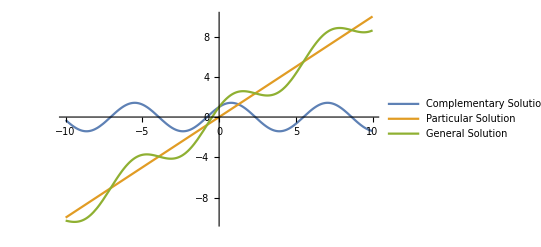

```mathematica
Plot[{Sin[x]+Cos[x],x,Sin[x]+Cos[x]+x},{x,-10,10},]
```

## Nonhomogeneous Equations

In the previous lesson, you solved every case of coefficients to the equation:

a y''(x)+b y'(x)+c y(x)=0

When the equation has a nonhomogeneous term:

a y''(x)+b y'(x)+c y(x)=g(x)

there are two important theorems that describe the form solutions take.

The first theorem states that when two functions Y_1(x), Y_2(x) are solutions to the nonhomogeneous equation, the difference Y_1(x)-Y_2(x) is a solution to the homogeneous equation.

## Theorem 1

Begin with a nonhomogeneous equation:

a y''(x)+b y'(x)+c y(x)=g(x)

Suppose two functions Y_1(x) and Y_2(x) are solutions to the nonhomogeneous equation and you want to show that their difference is a solution to the homogeneous equation:

a (Y_1(x)-Y_2(x))''+b (Y_1(x)-Y_2(x))'+c (Y_1(x)-Y_2(x))=0

a (Y_1''(x)-Y_2''(x))+b (Y_1'(x)-Y_2'(x))+c (Y_1(x)-Y_2(x))=0

[a Y_1''(x)+b Y_1'(x)+c Y_1(x)]-[a Y_2''(x)+b Y_2'(x)+c Y_2(x)]=0

The functions Y_1(t), Y_2(t) are solutions to the nonhomogeneous equation a y''(x)+b y'(x)+c y(x)=g(x), so these expressions can be correspondingly replaced:

g(x)-g(x)=0

You can see that the equation has been reduced to a trivially true equality.

The next theorem gives information about the form of solutions to nonhomogeneous equations.

## Theorem 2

The general solution to the nonhomogeneous equation a y''(x)+b y'(x)+c y(x)=g(x) can be written in the form:

y(x)=c_1 y_1(x)+c_2 y_2(x)+Y(x)

where y_1(x) and y_2(x) form a fundamental set of solutions of the corresponding homogeneous equation, C_1 and C_2 are arbitrary constants, and Y(x) is a solution to the nonhomogeneous equation:

```mathematica
Plot[{Sin[x]+Cos[x],x,Sin[x]+Cos[x]+x},{x,-10,10},]
```

-Graphics-

This is because a solution to the homogeneous equation always reduces to be zero when inserted into the nonhomogeneous differential equation, and thus it contributes nothing to the equality.

## Finding the General Solution

You saw that the difference of two solutions to the nonhomogeneous equation is a solution to the homogeneous equation:

Y_1(x)-Y_2(x)=c_1 y_1(x)+c_2 y_2(x)

This can always be reformulated as:

Y_1(x)=c_1 y_1(x)+c_2 y_2(x)+Y_2(x)

With this information, you know everything you need to do to solve the nonhomogeneous equation.

1. Find the solution to the homogeneous equation. This is often named the complementary solution.

2. Find any solution to the nonhomogeneous equation. This is named the particular solution.

3. The general solution is the sum of the two previous solutions.

## Basic Example

Find the general solution to the nonhomogeneous equation:

y''(x)+y(x)=x

First, solve the homogeneous equation:

y''(x)+y(x)=0

This has solution c_1 sin(x)+c_2 cos(x):

```mathematica
(y''[x]+y[x]==0)/.y->Function[x,Subscript[C, 1] Sin[x]+Subscript[C, 2] Cos[x]]
```

True

Thus the complementary solution is c_1 sin(x)+c_2 cos(x).

Next, you are searching for any function that satisfies the nonhomogeneous differential equation:

y''(x)+y(x)=x

By observation, one particular solution is y(x)=x because the second derivative is zero.

Thus, every solution to the nonhomogeneous differential equation takes the form:

c_1 sin(x)+c_2 cos(x)+x

## Basic Example

Confirm that the solution is indeed correct:

```mathematica
(y''[x]+y[x]==x)/.y->Function[x,Subscript[C, 1] Sin[x]+Subscript[C, 2] Cos[x]+x]
```

True

You can also compare your answer to the answer from DSolveValue:

```mathematica
DSolveValue[y''[x]+y[x]==x,y[x],x]
```

x+C[1] Cos[x]+C[2] Sin[x]

## Method of Undetermined Coefficients

This method is similar to the method of d’Alembert from the previous chapter.

Assume the function takes some form u(x) and insert this function into the equation to find the unknown function.

This lesson considers only nonhomogeneous terms that are polynomials, cosines, sines and exponential functions.

The particular solution that solves the nonhomogeneous equations often relates to the nonhomogeneous term.

## Example 1: Undetermined Coefficients

Find a particular solution to the equation:

y''(x)-3 y'(x)-4 y(x)=4 e^(2 x)

It is likely that the unknown function you are searching for is of the form A e^(2x):

```mathematica
(y''[x]-3 y'[x]-4 y[x]==4 Exp[2 x])/.y->Function[x,A Exp[2 x]]
```

-6 A ⅇ^(2 x)==4 ⅇ^(2 x)

The function appears to satisfy the differential equation when -6A=4.

It can be seen that A must be equal to -2/3:

```mathematica
(y''[x]-3 y'[x]-4 y[x]==4 Exp[2 x])/.y->Function[x,-2/3 Exp[2 x]]
```

True

Thus, you have found a particular solution.

## Example 2: Undetermined Coefficients

Find the general solution to the equation:

y''(x)-3 y'(x)-5 y(x)=2 sin(x)

Assume the function y(x) is of the form A sin(x) and substitute into the equation:

```mathematica
(y''[x]-3 y'[x]-5 y[x]==2 Sin[x])/.y->Function[x,A Sin[x]]
```

-3 A Cos[x]-6 A Sin[x]==2 Sin[x]

The function does not appear to satisfy the differential equation for any values of A.

Perhaps a better function to try is A sin(x)+B cos(x):

```mathematica
eqn=(y''[x]-3 y'[x]-5 y[x]==2 Sin[x])/.y->Function[x,A Sin[x]+B Cos[x]]
```

-B Cos[x]-A Sin[x]-5 (B Cos[x]+A Sin[x])-3 (A Cos[x]-B Sin[x])==2 Sin[x]

Collect the terms involving sin(x) and cos(x):

```mathematica
Collect[eqn,{Sin[x],Cos[x]}]
```

(-3 A-6 B) Cos[x]+(-6 A+3 B) Sin[x]==2 Sin[x]

Now you can observe two equations that the function must satisfy:

-3A-6B=0

-6A+3B=2

## Example 2: Undetermined Coefficients

You can use Solve to find the correct values for A and B:

```mathematica
Solve[{-3 A-6 B==0,-6 A+3 B==2},{A,B}]
```

{{A→-4/15,B→2/15}}

Verify that this solution satisfies the differential equation:

```mathematica
(y''[x]-3 y'[x]-5 y[x]==2 Sin[x])/.y->Function[x,-4/15 Sin[x]+2/15 Cos[x]]//Simplify
```

True

Thus, you have found a particular solution.

The complementary solution is found by solving for the roots of the characteristic polynomial.

## Example 2: Undetermined Coefficients

The characteristic polynomial is:

λ^2-3λ-5=0

The Roots of which are:

```mathematica
Roots[λ^2-3λ-5==0,λ]
```

λ==1/2 (3-√29)||λ==1/2 (3+√29)

Thus, the complementary solution is defined to be:

C_1 e^(1/2(3+√29)x)+C_2 e^(1/2(3-√29))

So the general solution is the sum of the complementary solution and any particular solution:

y(x)=-4/15sin(x)+2/15 cos(x)+C_1 e^(1/2(3+√29)x)+C_2 e^(1/2(3-√29))

```mathematica
sol=DSolveValue[y''[x]-3y'[x]-5y[x]==2Sin[x],y[x],x]//Simplify
```

ⅇ^(-1/2 (-3+√29) x) (C[1]+ⅇ^(√29 x) C[2])+(2 Cos[x])/15-(4 Sin[x])/15

Plot the various solutions using C_1=1/2 and C_2=1/3:

```mathematica
Plot[,{x,-1,.25},]
```

-Graphics-

## Summary of Undetermined Coefficients

For nonhomogeneous equations, the general solution is the sum of the complementary solution to the homogeneous equation and any particular solution to the nonhomogeneous equation.

The particular solution can be solved using the method of undetermined coefficients:

a y''(x)+b y'(x)+c y(x)=0

This involves making an inference about the form of the particular solution and solving for the coefficients so that it satisfies the initial conditions.

```mathematica
Plot[{Sin[x]+Cos[x],x,Sin[x]+Cos[x]+x},{x,-10,10},]
```

-Graphics-